```mathematica
(*ML Data*)

Data=Import["G:\\.shortcut-targets-by-id\\17WrugWUn3l1ON6QYmzE0UD-ifioHGbb0\\Priscila\\Research\\USMA\\New Approach\\COOLF1MathematicaReads.xlsx"];
(*Differences COOL F1 Score*)
ΔYVec=Data[[1,All,2]];

nΔYVec=Length[ΔYVec]
```

84

```mathematica
(*COOL F1 Score*)
YVec=Data[[1,All,1]];
n=Length[YVec]
```

84

```mathematica
(*fitting to % of the data*)
n90=Floor[nΔYVec (0.6)]
```

50

```mathematica
(*Covariates*)

(*Threshold*)
X1Vec=Data[[1,All,3]];

(*Length Train*)
X2Vec=Data[[1,All,4]];

(*Length Validation *)
X3Vec=Data[[1,All,5]];

(*Length Test*)
X4Vec=Data[[1,All,6]];

(*Validation Accuracy*)
X5Vec=Data[[1,All,7]];

(*Found Unkowns*)
X6Vec=Data[[1,All,8]];

(*Total Unkown Rate*)
X8Vec=Data[[1,All,10]];

(*Classes of Unkowns*)
X9Vec=Data[[1,All,11]];
```

```mathematica
(*Plot Y - Observed data*)
```

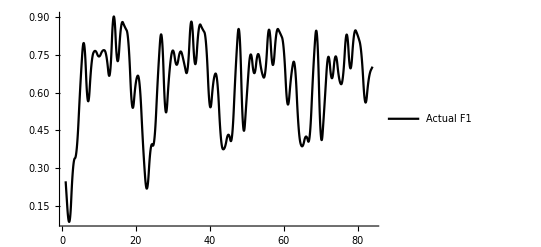

```mathematica
x=Table[i,{i,1,n}];
dataPlot=Transpose[{x,YVec}];
YObserved=ListPlot[dataPlot,InterpolationOrder->2, Joined->True,PlotRange->All,PlotStyle->Black,PlotLegends->{"Actual F1"}]
```

```mathematica
(* MLR*)
```

```mathematica
(*Normal Distribution*)
L=1/((2 π σ^2)^(n90/2))Exp[-1/(2 σ^2) (∑_(i=2)^n90 ((ΔYVec[[i]]-(β0+β1 X1[[i]] + β2 X2[[i]]+β3 X3[[i]] +β4 X4[[i]]+β7 X1[[i]] X2[[i]] + β8 X1[[i]] X3[[i]]+β9 X1[[i]] X4[[i]] +β12 X2[[i]] X3[[i]] +β13 X2[[i]] X4[[i]] +β16 X3[[i]] X4[[i]] +β21 YVec[[i-1]] +β22 X1[[i-1]]+β23 X2[[i-1]]+β24 X3[[i-1]]+β25 X4[[i-1]]))/.{X1->    X8Vec,X2-> X2Vec,X3->X3Vec,X4->X4Vec})^2)];
LnL=Log[L];


Dβ0=Simplify[D[LnL,β0]];
Dβ1=Simplify[D[LnL,β1]];
Dβ2=Simplify[D[LnL,β2]];
Dβ3=Simplify[D[LnL,β3]];
Dβ4=Simplify[D[LnL,β4]];


Dβ7=Simplify[D[LnL,β7]];
Dβ8=Simplify[D[LnL,β8]];
Dβ9=Simplify[D[LnL,β9]];


Dβ12=Simplify[D[LnL,β12]];
Dβ13=Simplify[D[LnL,β13]];


Dβ16=Simplify[D[LnL,β16]];




Dβ21=Simplify[D[LnL,β21]];
Dβ22=Simplify[D[LnL,β22]];
Dβ23=Simplify[D[LnL,β23]];
Dβ24=Simplify[D[LnL,β24]];
Dβ25=Simplify[D[LnL,β25]];


Dσ=Simplify[D[LnL,σ]];

RulesInt=FindRoot[{{0==Dβ0},{0==Dβ1},{0==Dβ2},{0==Dβ3},{0==Dβ4},{0==Dβ7},{0==Dβ8},{0==Dβ9},{0==Dβ12},{0==Dβ13},{0==Dβ16},{0==Dβ21},{0==Dβ22},{0==Dβ23},{0==Dβ24},{0==Dβ25},{0==Dσ}},{β0,0.1},{β1,0.1},{β2,0.1},{β3,0.1},{β4,0.1},{β7,0.1},{β8,0.1},{β9,0.1},{β12,0.1},{β13,0.1},{β16,0.1},{β21,0.1},{β22,0.1},{β23,0.1},{β24,0.1},{β25,0.1},{σ,0.1}, MaxIterations->1000]//Quiet
```

Part::partd: Part specification X1⟦2⟧ is longer than depth of object.

Part::partd: Part specification X2⟦2⟧ is longer than depth of object.

Part::partd: Part specification X3⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{β0→-1204.33,β1→12.0496,β2→0.613307,β3→-0.427549,β4→0.188932,β7→0.0244087,β8→-0.0794631,β9→-0.0018742,β12→-0.000135293,β13→-0.000422113,β16→0.00114466,β21→-0.372705,β22→-0.0955555,β23→-0.108784,β24→0.320135,β25→-0.000239374,σ→7.49319×10^102}

```mathematica
(*Prediction*)
LRInt=β0+β1 X1[[i]] + β2 X2[[i]]+β3 X3[[i]] +β4 X4[[i]]+β7 X1[[i]] X2[[i]] + β8 X1[[i]] X3[[i]]+β9 X1[[i]] X4[[i]] +β12 X2[[i]] X3[[i]] +β13 X2[[i]] X4[[i]] +β16 X3[[i]] X4[[i]] +β21 YVec[[i-1]] +β22 X1[[i-1]]+β23 X2[[i-1]]+β24 X3[[i-1]]+β25 X4[[i-1]]  ;
LRInt=LRInt/.RulesInt; 

YFitListInt=.
YFitListInt={ΔYVec[[1]]};
For[k=2,k<=nΔYVec,
AppendTo[YFitListInt,LRInt/.{X1->    X8Vec,X2-> X2Vec,X3->X3Vec,X4->X4Vec,i->k}]//Quiet;
k=k+1;
];
YFitListInt
```

Part::pkspec1: The expression i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::pkspec1: The expression -1+i cannot be used as a part specification.

{0.,-0.051033,0.186323,0.0288604,0.285202,0.133215,-0.252642,0.156382,0.0188273,-0.000789749,0.00142821,-0.00886923,-0.0572529,0.208103,-0.171594,0.178577,-0.0570844,-0.0660813,-0.228116,0.0403188,-0.000465978,-0.243854,-0.0985263,0.13734,-0.000287873,0.271172,0.117869,-0.263072,0.1708,0.0353392,-0.00139832,0.0136502,-0.0074225,-0.0474023,0.201667,-0.164181,0.183213,-0.0532398,-0.0630308,-0.226443,0.0397999,-0.00249212,-0.248155,-0.114506,0.0773047,-0.0210199,0.266671,0.110292,-0.268399,0.194116,0.0653685,0.00467936,0.0260235,-0.00380189,-0.0348308,0.206219,-0.152237,0.184611,-0.0472002,-0.0567134,-0.218984,0.0366082,-0.00983097,-0.270084,-0.130379,0.0751569,-0.0183362,0.266512,0.109728,-0.264302,0.206588,0.0792224,0.00827838,0.0335325,-0.00057073,-0.0230346,0.213331,-0.145023,0.189766,-0.0451564,-0.0530891,-0.212191,0.0338856,-0.0062532}

```mathematica
YFitCumulativeInt=.
YFitCumulativeInt={YVec[[1]]+YFitListInt[[1]]};
For[k=1,k<(nΔYVec),
AppendTo[YFitCumulativeInt,(YFitCumulativeInt[[k]]+YFitListInt[[k+1]])]//Quiet;
k=k+1;
];
YFitCumulativeInt
```

{0.249077,0.198044,0.384366,0.413226,0.698429,0.831644,0.579002,0.735384,0.754212,0.753422,0.75485,0.745981,0.688728,0.896831,0.725237,0.903813,0.846729,0.780648,0.552532,0.592851,0.592385,0.348531,0.250005,0.387344,0.387057,0.658228,0.776097,0.513025,0.683825,0.719164,0.717766,0.731416,0.723993,0.676591,0.878258,0.714077,0.897291,0.844051,0.78102,0.554576,0.594376,0.591884,0.343729,0.229223,0.306528,0.285508,0.552179,0.662471,0.394072,0.588188,0.653557,0.658236,0.684259,0.680458,0.645627,0.851846,0.699609,0.88422,0.83702,0.780307,0.561323,0.597931,0.5881,0.318016,0.187638,0.262794,0.244458,0.51097,0.620698,0.356396,0.562985,0.642207,0.650485,0.684018,0.683447,0.660412,0.873743,0.72872,0.918486,0.87333,0.820241,0.60805,0.641935,0.635682}

```mathematica
failureCount = Table[index,{index,1,n}];
NewPlot=Transpose[{failureCount,YFitCumulativeInt}]
```

{{1,0.249077},{2,0.198044},{3,0.384366},{4,0.413226},{5,0.698429},{6,0.831644},{7,0.579002},{8,0.735384},{9,0.754212},{10,0.753422},{11,0.75485},{12,0.745981},{13,0.688728},{14,0.896831},{15,0.725237},{16,0.903813},{17,0.846729},{18,0.780648},{19,0.552532},{20,0.592851},{21,0.592385},{22,0.348531},{23,0.250005},{24,0.387344},{25,0.387057},{26,0.658228},{27,0.776097},{28,0.513025},{29,0.683825},{30,0.719164},{31,0.717766},{32,0.731416},{33,0.723993},{34,0.676591},{35,0.878258},{36,0.714077},{37,0.897291},{38,0.844051},{39,0.78102},{40,0.554576},{41,0.594376},{42,0.591884},{43,0.343729},{44,0.229223},{45,0.306528},{46,0.285508},{47,0.552179},{48,0.662471},{49,0.394072},{50,0.588188},{51,0.653557},{52,0.658236},{53,0.684259},{54,0.680458},{55,0.645627},{56,0.851846},{57,0.699609},{58,0.88422},{59,0.83702},{60,0.780307},{61,0.561323},{62,0.597931},{63,0.5881},{64,0.318016},{65,0.187638},{66,0.262794},{67,0.244458},{68,0.51097},{69,0.620698},{70,0.356396},{71,0.562985},{72,0.642207},{73,0.650485},{74,0.684018},{75,0.683447},{76,0.660412},{77,0.873743},{78,0.72872},{79,0.918486},{80,0.87333},{81,0.820241},{82,0.60805},{83,0.641935},{84,0.635682}}

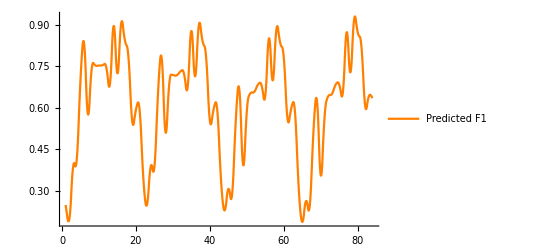

```mathematica
YPredictedPlotInt=ListPlot[(NewPlot),InterpolationOrder->2, Joined->True,PlotStyle->Orange,PlotRange->All,PlotLegends->{"Predicted F1"}]
```

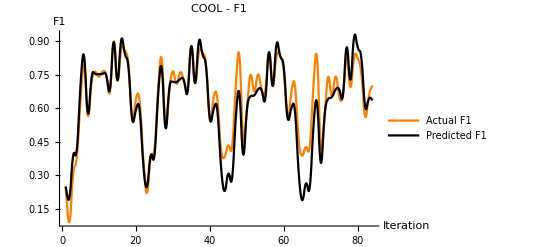

```mathematica
(*Comparing Y observed vs Y predicted with multiple linear regression*)
A=ListPlot[{dataPlot,NewPlot},InterpolationOrder->2, Joined->True,PlotStyle->{Orange,Black},PlotRange->All,PlotLegends->{"Actual F1","Predicted F1"},PlotLabel->"COOL - F1",AxesLabel->{"Iteration","F1"}]
```

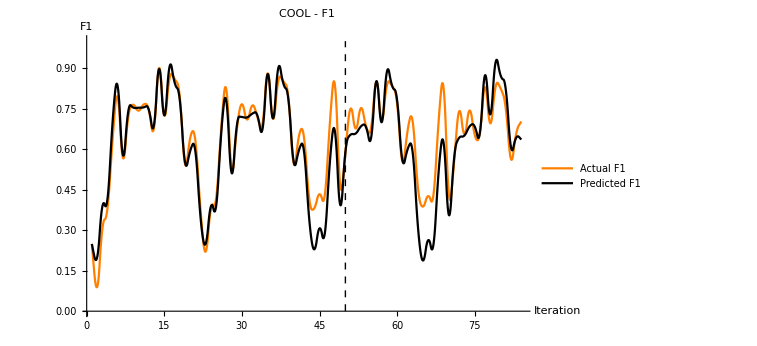

```mathematica
B=Graphics[{Black, Dashed,Line[{{n90,0},{n90,1}}]}];
Show[A,B]
```

```mathematica
(*Measure of the quality of the fit (page 60) *)

(*Prediction of Y using X*)
```

```mathematica
(*SSE*)
```

```mathematica
(*SSE=∑_(i=1)^nΔYVec (ΔYVec[[i]]-YFitListInt[[i]])^2*)
```

```mathematica
SSE=∑_(i=1)^nΔYVec (YVec[[i]]-YFitCumulativeInt[[i]])^2
```

0.447997

```mathematica
(*PSSE*)
```

```mathematica
(*PSSE=∑_(i=n90+1)^nΔYVec (ΔYVec[[i]]-YFitListInt[[i]])^2*)
```

```mathematica
PSSE=∑_(i=n90+1)^nΔYVec (YVec[[i]]-YFitCumulativeInt[[i]])^2
```

0.277919

```mathematica
(*variance*)
```

```mathematica
S2=1/(n-2)(SSE);
```

```mathematica
(*Mean Squared Error*)
MSE=SSE/n;
```

```mathematica
(*Mean Squared Error Predicte data*)
MSEP=PSSE/(n-n90+1)
```

0.00794054

```mathematica
(*Correlation Coefficient*)
```

```mathematica
(*prediction of Y if X is ignored*)
```

```mathematica
SSY=∑_(i=1)^nΔYVec (ΔYVec[[i]]-Mean[ΔYVec])^2;
```

```mathematica
(*values between 0 and 1. The larger the value of r2, the stronger the linear regression between X and Y*)
```

```mathematica
r2=(SSY-SSE)/SSY;
```

```mathematica
(*p is the number of independent variables in the model (excluding the constant term)*)
```

```mathematica
r2Adj=1-(1-r2)(n-1)/(n-p-1)/.p->16
```

0.698101